## ALPs coupled to gluons

```mathematica
LLPsel="ALP-gluon";
ModelDescription[LLPsel]=Row[{"Axion-like particle a with the phenomenological Lagrangian L = c_Ga/f_aα_S/(4  π)G^μν(G̃)_μν. The Lagrangian is defined at some scale Λ, with c_G, f_a being the couplings (f_a is in general unrelated to Λ). G_μν is the SM gluon field, and (G̃)_μν is its dual. The RG flow down to scales of interest induces small couplings to quarks. For the particular choice Λ = 1 TeV and c_G = 1, the model is called BC11 within PBC benchmarking (1901.09966). See 2110.10698, 2310.03524, and 2501.04525 for the phenomenology description"}];
filepheno=FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology","ModelDescriptors.mx"}];
rowtoadd={LLPsel,ModelDescription[LLPsel]};
If[!FileExistsQ[filepheno],
file={rowtoadd};
,
file=Import[filepheno,"MX"];
file=Join[Select[file,#[[1]]!=LLPsel&],{rowtoadd}];
]
Export[filepheno,SortBy[file,#[[1]]&],"MX"];
```

### Importing lifetime

```mathematica
LLPsel="ALP-gluon";
(*List of widths of the ALP into various final states*)
DecayWidthsDataTemp=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology",LLPsel,"decay widths","Widths-model-Gluon-scale-1000.-GeV.m"}],"MX"];
DecayWidthsDataTemp2=DecayWidthsDataTemp[[4]];
{Table[i,{i,1,Length[DecayWidthsDataTemp2[[1]]],1}],DecayWidthsDataTemp2[[1]]}//TableForm
DecayWidthsData=Drop[DecayWidthsDataTemp2,3];
(*Total decay width and lifetime*)
totalwidthdata=DecayWidthsData[[All,{1,-1}]];
descr="Default";
cτLLP[LLPsel,descr,mLLP_,finv_]=chbar/(finv^2*Interpolation[DecayWidthsData[[All,{1,-1}]],InterpolationOrder->1][mLLP]);
couplingSymbol[LLPsel]=finv;
DecayDescriptionExplanation[LLPsel,descr]="Description of hadronic width of ALPs following 2310.03524";
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34
m_a, GeV | 2e | 2γ | 2μ | 2τ | 2b | 2c | 2d | 2G | 2s | 2t | 2u | 2π^+2π^- | 2ϕ | 2ω | 3π^0 | 3η | K^(*0)(K̄)^(*0) | K^0(K̄)^0π^0 | K^(*+)K^(*-) | K^-K^0π^+ | K^+K^-π^0 | K^+(K̄)^0π^- | γπ^+π^- | η2π^0 | ηπ^+π^- | π^+π^-2π^0 | π^+π^-π^0 | ωπ^+π^- | η'2π^0 | η'π^+π^- | Non-hadronic, total | Hadronic, total | Total

### List of decay processes and sets of decay products for them, branching ratios

2e | 2μ | 2τ | 2γ | π^+π^-π^0 | γπ^+π^- | π^+π^-2π^0 | 2π^+2π^- | η2π^0 | ηπ^+π^- | K^(*+)K^(*-) | K^(*0)(K̄)^(*0) | K^0(K̄)^0π^0 | K^-K^0π^+ | K^+K^-π^0 | K^+(K̄)^0π^- | ωπ^+π^- | 3π^0 | η'2π^0 | η'π^+π^- | 2ω | Jets-GG | Jets-cc | Jets-ss
e^+
e^-
Null
Null | μ^+
μ^-
Null
Null | τ^+
τ^-
Null
Null | γ
γ
Null
Null | π^+
π^-
π^0
Null | π^+
π^-
γ
Null | π^+
π^0
π^-
π^0 | π^+
π^-
π^+
π^- | η
π^0
π^0
Null | η
π^+
π^-
Null | K^(*+)
K^(*-)
Null
Null | K^(*0)
(K̄)^(*0)
Null
Null | K_L
K_S
π^0
Null | K^-
K_L
π^+
Null | K^+
K^-
π^0
Null | K^+
K_S
π^-
Null | ω
π^+
π^-
Null | π^0
π^0
π^0
Null | η'
π^0
π^0
Null | η'
π^+
π^-
Null | ω
ω
Null
Null | g
ḡ
Null
Null | c
c̄
Null
Null | s
s̄
Null
Null

All processes with at least two charged/neutral particles:

{2e,2μ,2τ,2γ,π^+π^-π^0,γπ^+π^-,π^+π^-2π^0,2π^+2π^-,η2π^0,ηπ^+π^-,K^(*+)K^(*-),K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,ωπ^+π^-,3π^0,η'2π^0,η'π^+π^-,2ω,Jets-GG,Jets-cc,Jets-ss}

All processes with at least two charged particles:

{2e,2μ,2τ,π^+π^-π^0,γπ^+π^-,π^+π^-2π^0,2π^+2π^-,η2π^0,ηπ^+π^-,K^(*+)K^(*-),K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,ωπ^+π^-,η'2π^0,η'π^+π^-,2ω,Jets-GG,Jets-cc,Jets-ss}

Processes with jets:

{Jets-GG,Jets-cc,Jets-ss}

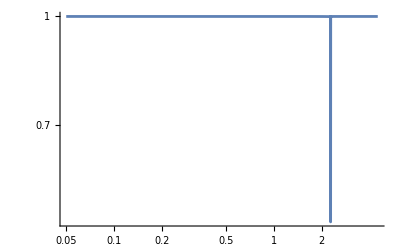

```mathematica
LLPsel="ALP-gluon";
BrRatiosALPgluonData[ma_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology",LLPsel,"decay widths/Br-ratios-SensCalc-model-Gluon-scale-1000.-GeV.m"}],"MX"];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=BrRatiosALPgluonData[ma][[1]]/.{"Jets"->"Jets-GG"};
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
procsel=ProcessesList[LLPsel,"True"][[i]];
ListBrRatiosTemp[LLPsel,mLLP_,procsel,"Default"]=ListBrRatios[LLPsel,mLLP_,procsel,"Default"]=BrRatiosALPgluonData[mLLP][[3]][[i]];
ListDecayProducts[LLPsel,procsel]=BrRatiosALPgluonData[ma][[2]][[i]];
JetsPresence[LLPsel,procsel]=If[MemberQ[{"Jets-ss","Jets-cc","Jets-GG"},procsel]==True,"Yes","No"]
,{i,1,Length[BrRatiosALPgluonData[mLLP][[3]]],1}]
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel];
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm
Print["All processes with at least two charged/neutral particles:"]
ProcessesList[LLPsel,"True"]
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatiosTemp[LLPsel,mN,pr,"Default"],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,4.5},PlotRange->All]
listDecayDescriptions[LLPsel]=Select[Transpose[Keys[DownValues@ListBrRatios][[All,1,#]]&/@{1,-1}],#[[1]]==LLPsel&][[All,2]]//DeleteDuplicates
```

### Squared matrix elements

```mathematica
LLPsel="ALP-gluon";
MatrixElementsALPgluonList[ma_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology",LLPsel,"decay widths/Matrix-elements-squared-model-Gluon-scale-1000.-GeV.m"}],"MX"];
Do[
Msquared3BodyLLP[LLPsel,MatrixElementsALPgluonList[ma][[1]][[i]],E1_,E3_,mLLP_,"Default"]=MatrixElementsALPgluonList[mLLP][[3]][[i]]
,{i,1,Length[MatrixElementsALPgluonList[ma][[3]]],1}];
```